```mathematica
Clear["Global`*"];
Off[General::spell];
Off[General::spell1];
```

```mathematica
m=3;
d=5;
```

```mathematica
sol=ParametricNDSolve[{
x'[t]==v[t],
v'[t]==m*(1-x[t]^2)*v[t]-x[t]+d*Cos[w*t],
x[0]==0,
v[0]==0
},{x,v},{t,300,400},{w}]
```

{x→ParametricFunction[<>],v→ParametricFunction[<>]}

```mathematica
solutions=Evaluate[Table[{x->(x[w][t]/.sol),v->(v[w][t]/.sol)},{w,{20,5,2,1.788,1}}]]
```

{{x→InterpolatingFunction[{{300., 400.}}, <>][t],v→InterpolatingFunction[{{300., 400.}}, <>][t]},{x→InterpolatingFunction[{{300., 400.}}, <>][t],v→InterpolatingFunction[{{300., 400.}}, <>][t]},{x→InterpolatingFunction[{{300., 400.}}, <>][t],v→InterpolatingFunction[{{300., 400.}}, <>][t]},{x→InterpolatingFunction[{{300., 400.}}, <>][t],v→InterpolatingFunction[{{300., 400.}}, <>][t]},{x→InterpolatingFunction[{{300., 400.}}, <>][t],v→InterpolatingFunction[{{300., 400.}}, <>][t]}}

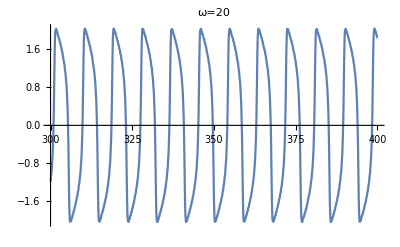

```mathematica
Show[Plot[x/.solutions[[1]],{t,300,400},PlotRange->All],PlotLabel->"ω=20"]
```

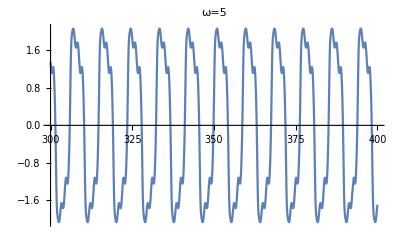

```mathematica
Show[Plot[x/.solutions[[2]],{t,300,400},PlotRange->All],PlotLabel->"ω=5"]
```

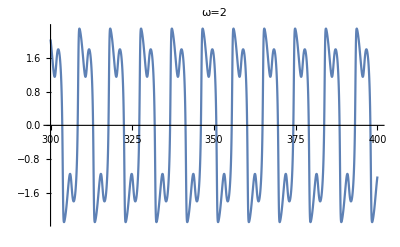

```mathematica
Show[Plot[x/.solutions[[3]],{t,300,400},PlotRange->All],PlotLabel->"ω=2"]
```

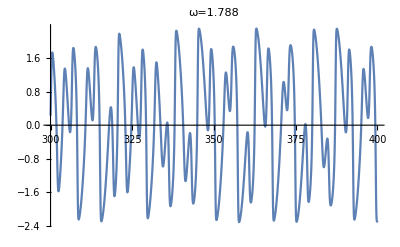

```mathematica
Show[Plot[x/.solutions[[4]],{t,300,400},PlotRange->All],PlotLabel->"ω=1.788"]
```

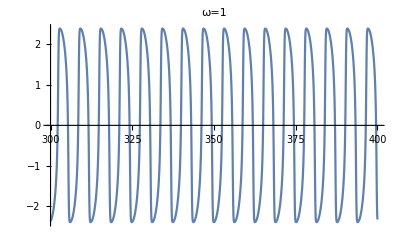

```mathematica
Show[Plot[x/.solutions[[5]],{t,300,400},PlotRange->All],PlotLabel->"ω=1"]
```

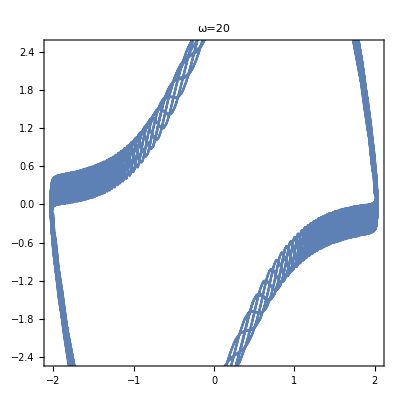

```mathematica
Show[ParametricPlot[{x/.solutions[[1]],v/.solutions[[1]]},{t,300,400}],
PlotLabel->"ω=20",
Frame -> True, 
AspectRatio -> 1]
```

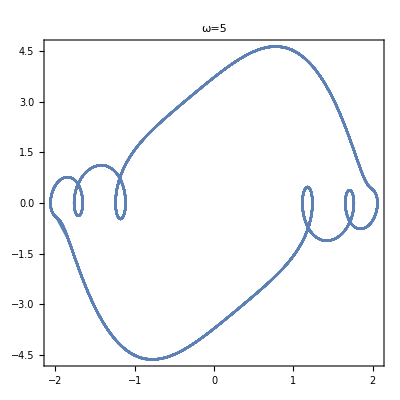

```mathematica
Show[ParametricPlot[{x/.solutions[[2]],v/.solutions[[2]]},{t,300,400}],
PlotLabel->"ω=5",
Frame -> True, 
AspectRatio -> 1]
```

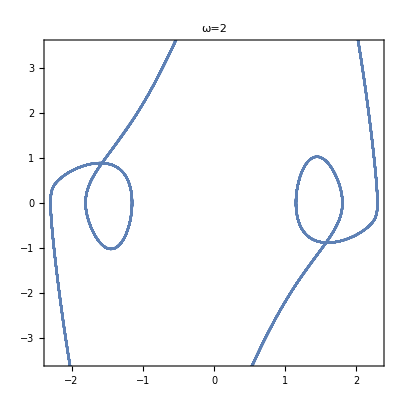

```mathematica
Show[ParametricPlot[{x/.solutions[[3]],v/.solutions[[3]]},{t,300,400}],
PlotLabel->"ω=2",
Frame -> True, 
AspectRatio -> 1]
```

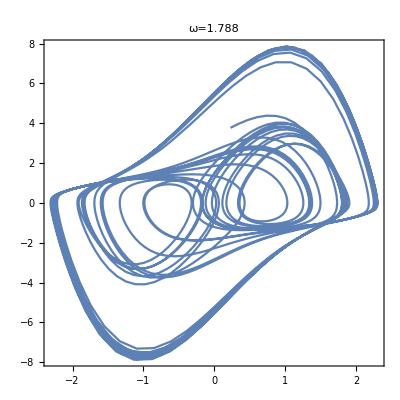

```mathematica
Show[ParametricPlot[{x/.solutions[[4]],v/.solutions[[4]]},{t,300,400}],
PlotLabel->"ω=1.788",
Frame -> True, 
AspectRatio -> 1]
```

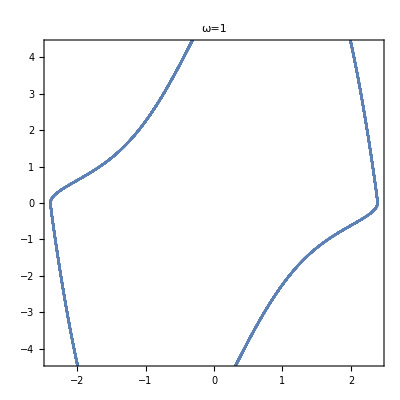

```mathematica
Show[ParametricPlot[{x/.solutions[[5]],v/.solutions[[5]]},{t,300,400}],
PlotLabel->"ω=1",
Frame -> True, 
AspectRatio -> 1]
```

```mathematica
poincare[w_, ndrop_, nplot_, psize_] := (
T = 2 π/w; 
g[{xnew_, vnew_}] := {x[T], v[T]} /. 
	Flatten [ 
NDSolve[{
x'[t]==v[t],
v'[t]==m*(1-x[t]^2)*v[t]-x[t]+d*Cos[w*t],
x[0]==xnew,
v[0]==vnew
},{x,v},{t,0,T}]
] ;
ListPlot[ 
Drop[ 
NestList[g, {0, 0}, nplot+ndrop],ndrop],
PlotStyle -> PointSize[psize],
PlotRange->{{-3,3},{-3,3}} , 
AxesLabel -> {"x", "v"} 
] 
)
```

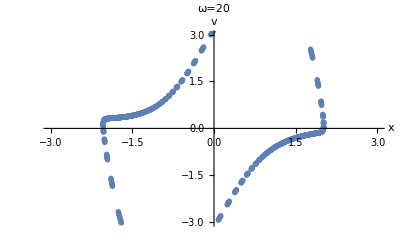

```mathematica
Show[poincare[20,800,1000,0.01],PlotLabel->"ω=20"]
```

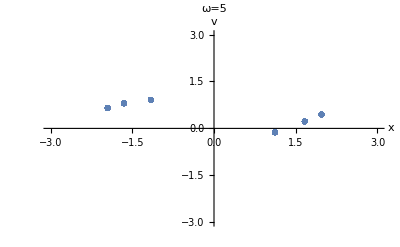

```mathematica
Show[poincare[5,800,1000,0.01],PlotLabel->"ω=5"]
```

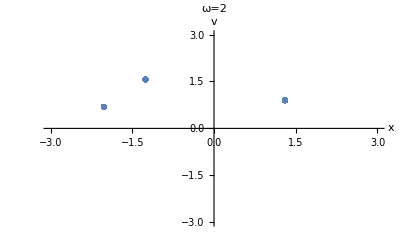

```mathematica
Show[poincare[2,800,1000,0.01],PlotLabel->"ω=2"]
```

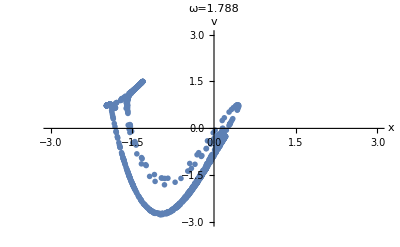

```mathematica
Show[poincare[1.788,800,1000,0.01],PlotLabel->"ω=1.788"]
```

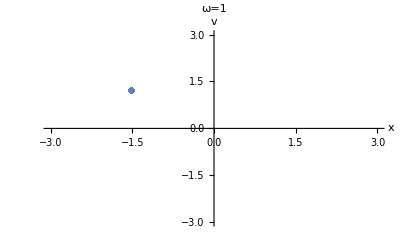

```mathematica
Show[poincare[1,800,1000,0.01],PlotLabel->"ω=1"]
```